```mathematica
ϵ=0
```

0

```mathematica
g1=x1^2+(5(x2-3)/4-Sqrt[x1^2+ϵ])^2
```

x1^2+(-√(x1^2)+5/4 (-3+x2))^2

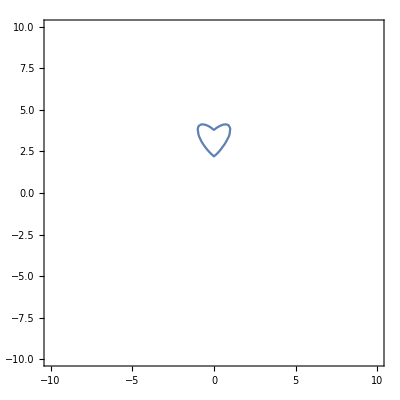

```mathematica
OstrovA=ContourPlot[g1==1,{x1,-10,10}, {x2,-10,10}]
```

```mathematica
g2=(2(y1-3)^2+2(y2-4)^2)^3-40(y1-3)^2(y2-4)^2
```

(2 (-3+y1)^2+2 (-4+y2)^2)^3-40 (-3+y1)^2 (-4+y2)^2

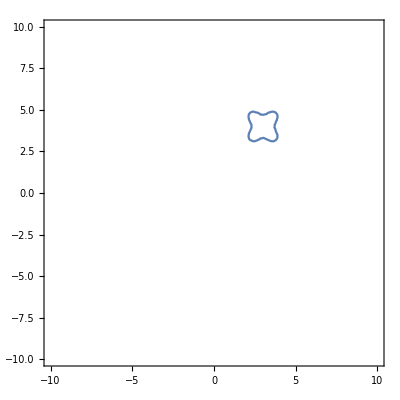

```mathematica
OstrovB=ContourPlot[g2==1, {y1,-10,10}, {y2,-10,10}]
```

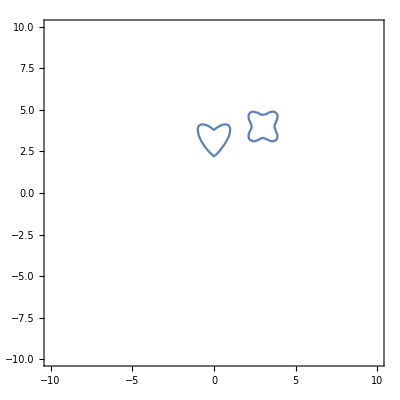

```mathematica
Show[OstrovA,OstrovB]
```

```mathematica
f=(x1-y1)^2+(x2-y2)^2
```

1.29599

```mathematica
1.2959893233490003
```

1.29599

```mathematica
Minimum= FindMinimum[{f, g1≤1, g2≤1},{x1,y1,x2,y2}](*Pre lepšiu konvergenciu Newtonovej metódy hľadáme minimum tejto funkcie namiesto odmocniny*)
```

FindMinimum[{f,g1≤1,g2≤1},{x1,y1,x2,y2}]

```mathematica
x1=0.988257
```

0.988257

```mathematica
y1=2.11105
```

2.11105

```mathematica
x2=3.66837
```

3.66837

```mathematica
y2=3.48042
```

3.48042

```mathematica
A=Point[{x1,x2}]
```

Point[{0.988257,3.66837}]

```mathematica
B=Point[{y1,y2}]
```

Point[{2.11105,3.48042}]

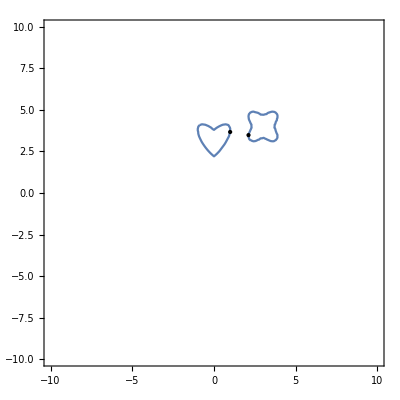

```mathematica
Show[OstrovA,OstrovB,
Graphics[A],
Graphics[B]


]
```

```mathematica
line=Graphics[{RGBColor[1, 0, 0], Line[{A, B}]}]
```

-Graphics-

```mathematica
Show[line, Axes->True, AxesLabel->{x,y}]
```

-Graphics-